```mathematica
bifurcation[xmin_,xmax_,step_]:=Module[{equ,tfpt,truncated,fp,coords},
equ=Solve[x-(x+d)^3==0,x];
tfpt=Table[x/.#1&/@equ,{d,xmin,xmax,step}];
truncated[a_]:=Module[{reim,new},
reim=ReIm[a];
new=If[Abs[#1]<10^-8,#1/.#1-> 0,#1]&/@reim;
new[[1]]+new[[2]]I];
fp=Map[truncated,tfpt,{2}]//.{c___,a_Complex,b___} -> {c,Nothing,b};
coords=Flatten[Table[{Range[xmin,xmax,step][[i]],#1}&/@fp[[i]],{i,1,Length[fp]}],1];
ListPlot[coords,PlotRange-> All,PlotLabel-> Style["Bifurcation Diagram",Larger],AxesLabel-> {Style["d",Medium],Style["x",Medium]},ClippingStyle-> Red]]
```

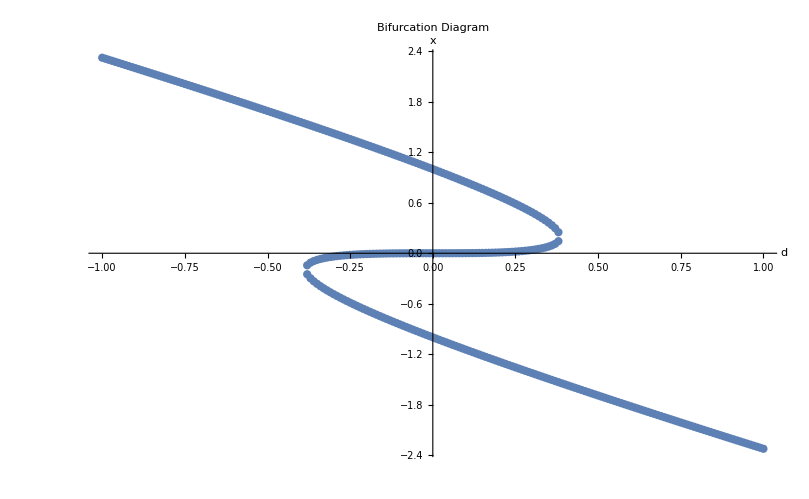

```mathematica
bifurcation[-1,1,0.01]
```

```mathematica
bifurcation1[xmin_,xmax_,step_]:=Module[{equ,tfpt,truncated,fp,trunc,coords},
equ=Solve[x-(x+d)^3==0,x];
tfpt=Table[x/.#1&/@equ,{d,xmin,xmax,step}];
truncated[a_]:=Module[{reim,new},
reim=ReIm[a];
new=If[Abs[#1]<10^-8,#1/.#1-> 0,#1]&/@reim;
new[[1]]+new[[2]]I];
fp=Map[truncated,tfpt,{2}](*//.{c___,a_Complex,b___} -> {c,Nothing,b}*);
coords=Table[{Range[xmin,xmax,step][[i]],#1}&/@fp[[i]],{i,1,Length[fp]}];
(*ListPlot[coords,PlotRange-> All,PlotLabel-> Style["Bifurcation Diagram",Larger],AxesLabel-> {Style["d",Medium],Style["x",Medium]},ClippingStyle-> Red,PlotStyle-> {Dashed}]*)
ListPlot[Table[Table[{Range[-1,1,0.1][[i]],Transpose[fp][[j]][[i]]},{i,1,Length[fp]}],{j,1,3}],PlotRange-> All,PlotStyle-> {Directive[CMYKColor[{1,0.5,0.5,0}],PointSize[0.007]],Directive[CMYKColor[{1,0.5,0.5,0}],PointSize[0.007]],Directive[Darker[Red],PointSize[0.007]]},AxesLabel-> {Style["d",Medium],Style["x",Medium]},PlotLabel-> Style["Bifurcation Diagram",Larger]]]
```

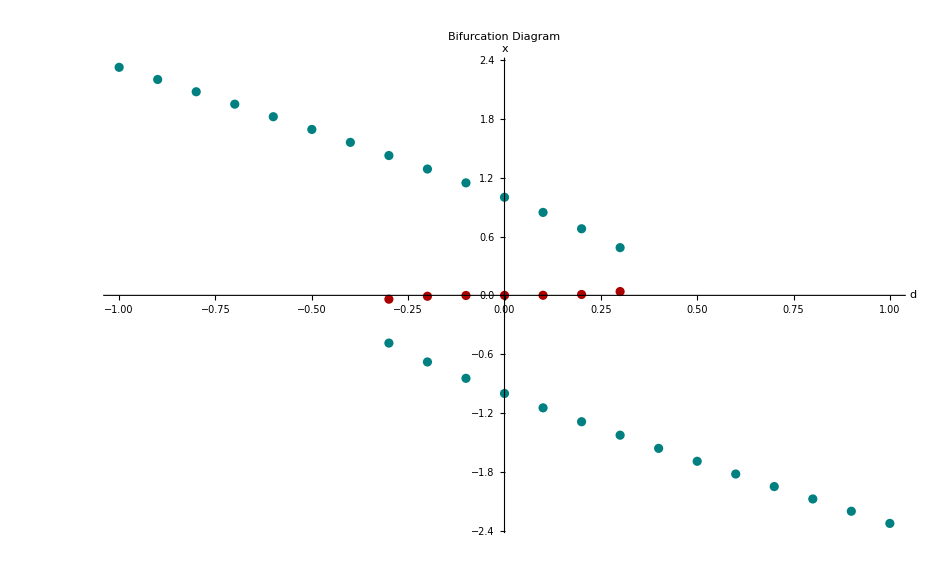

```mathematica
bifurcation1[-1,1,0.1]
```